## Correlator ,⟨∂ϕ∂ϕ∂ϕ∂ϕ⟩ in the free boson theory

### Conformal blocks in position space

```mathematica
g[h_][z_]=z^h Hypergeometric2F1[h,h,2h,z];
```

### Conformal blocks in momentum space

```mathematica
SetDirectory[NotebookDirectory[]];
<<MSCB2d`
```

MSCB2d is a Mathematica package that evaluates
Momentum-Space Conformal Blocks in a 2d CFT.

The Wightman 4-point function
  ⟨Ω|O_4(p_4)O_3(p_3)O_2(p_2)O_1(p_1)|Ω⟩
    = (2π)^2 δ(p_1+p_2+p_3+p_4) G(p_a)
admits the conformal block expansion
  G(p_a)=∑_x  λ_(12  x)λ_x34 G_x(p_a)
This package provides explicit expressions for G_x
as a function of the conformal weights (h_a,(h̄)_a) of
the external (1,2,3,4) and exchange (x) operators
and of the momenta p_a.

The following conventions are used for the momenta:
  p_i=p_1   
  p_f=-p_4
  k=p_1+p_2=-p_3-p_4
The 4-point function is identically zero unless
all 3 momenta p_i, p_f and k lie in the future
light-cone.

### Correlation function in position space

```mathematica
G[z_]=1+z^2+z^2/(1-z)^2;
```

```mathematica
Simplify[1/((z1-z2)^2(z3-z4)^2)G[((z1-z2)(z3-z4))/((z1-z3)(z2-z4))]==1/((z1-z2)^2(z3-z4)^2)+1/((z1-z3)^2(z2-z4)^2)+1/((z1-z4)^2(z2-z3)^2),z1>z2>z3>z4]
```

True

### Conformal block expansion in position space

Operators contributing to the 4-point function are:
1) The identity with conformal weight (0,0) and OPE coefficient 1
2) A series of operators with conformal weights (h=2n,0) and OPE coefficients:

```mathematica
λ[h_]:=((h-1)!h!)/((2h-3)!)
```

```mathematica
Series[G[z],{z,0,20}]
Series[g[0][z]+Sum[λ[h]g[h][z],{h,2,20,2}],{z,0,20}]
%%==%
```

1+2 z^2+2 z^3+3 z^4+4 z^5+5 z^6+6 z^7+7 z^8+8 z^9+9 z^10+10 z^11+11 z^12+12 z^13+13 z^14+14 z^15+15 z^16+16 z^17+17 z^18+18 z^19+19 z^20+O[z]^21

1+2 z^2+2 z^3+3 z^4+4 z^5+5 z^6+6 z^7+7 z^8+8 z^9+9 z^10+10 z^11+11 z^12+12 z^13+13 z^14+14 z^15+15 z^16+16 z^17+17 z^18+18 z^19+19 z^20+O[z]^21

True

Asymptotic behavior of the OPE coefficients:

```mathematica
Table[λ[h],{h,2,20,2}]
```

{2,6/5,5/21,14/429,9/2431,11/29393,13/371450,2/646323,17/64822395,19/883631595}

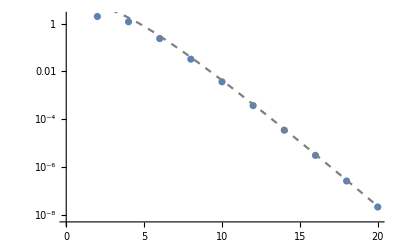

```mathematica
Show[ListLogPlot[Table[{h,λ[h]},{h,2,20,2}]],LogPlot[(√π h^(5/2))/2^(2h-3),{h,2,20},PlotStyle->{Gray,Dashed}]]
```

### Conformal block expansion in momentum space

```mathematica
Wsum[n_][pf_,k_,pi_]:=Sum[λ[h]HolomorphicCB[1,h][-pf,k,pi],{h,2,n,2}]
```

```mathematica
plot3d8=Plot3D[(Wsum[8][pf,1,pi])/(2π)^4,{pi,0,1.2},{pf,0,1.2},PlotRange->All,Boxed->False,ColorFunction->"TemperatureMap",AxesLabel->{"p_i/k","p_f/k",""},BaseStyle->{14,FontFamily->"Latin Modern Roman"},PlotLabel->"4 operators"]
```

-Graphics3D-

```mathematica
plot3d16=Plot3D[(Wsum[16][pf,1,pi])/(2π)^4,{pi,0,1.2},{pf,0,1.2},PlotRange->All,Boxed->False,ColorFunction->"TemperatureMap",AxesLabel->{"p_i/k","p_f/k",""},BaseStyle->{14,FontFamily->"Latin Modern Roman"},PlotLabel->"8 operators"]
```

-Graphics3D-

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["FreeScalar_delta_1.pdf",plot3d8]
Export["FreeScalar_delta_2.pdf",plot3d16]*)
```

```mathematica
(*nmax=10;
plot3dtable=Table[Plot3D[(Wsum[2n][pf,1,pi])/(Wsum[2n][1/2,1,1/2]),{pi,0,1.2},{pf,0,1.2},PlotRange->{Automatic,Automatic,{-0.25,1}},Boxed->False,ColorFunction->"TemperatureMap",AxesLabel->{"p_i/k","p_f/k",""},BaseStyle->{14,FontFamily->"Latin Modern Roman"},PlotLabel->ToString[n]<>" operators"],{n,nmax}];
SetDirectory[NotebookDirectory[]];
Export["FreeScalar_delta.gif",plot3dtable,"DisplayDurations"->Table[1+KroneckerDelta[i,nmax],{i,nmax}]]*)
```

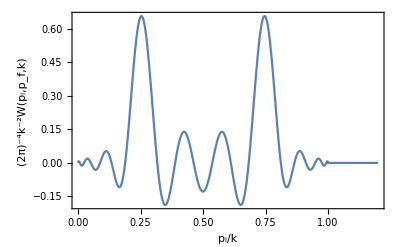

```mathematica
plot20=Plot[(Wsum[20][1/4,1,pi])/(2π)^4,{pi,0,1.2},PlotRange->{{0,1.2},All},Axes->False,Frame->True,FrameLabel->{"p_i/k","(2π)^-4k^-2W(p_i,p_f,k)","k = 4 p_f      10 operators"},BaseStyle->{14,FontFamily->"Latin Modern Roman"}]
```

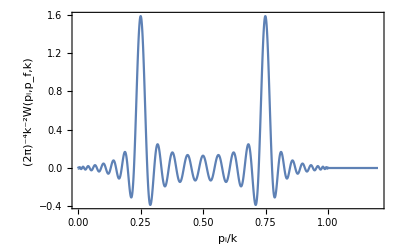

```mathematica
plot50=Plot[(Wsum[50][1/4,1,pi])/(2π)^4,{pi,0,1.2},PlotRange->{{0,1.2},All},Axes->False,Frame->True,FrameLabel->{"p_i/k","(2π)^-4k^-2W(p_i,p_f,k)","k = 4 p_f      25 operators"},BaseStyle->{14,FontFamily->"Latin Modern Roman"}]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["FreeScalar_delta_3.pdf",plot20]
Export["FreeScalar_delta_4.pdf",plot50]*)
```

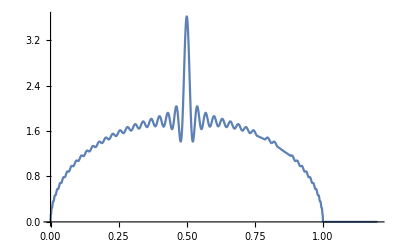

```mathematica
Plot[(Wsum[50][p,1,p])/(2π)^4,{p,0,1.2}]
```

Integration :

```mathematica
Table[Integrate[Wsum[hmax][1/4,1,pi],{pi,0,1/2}],{hmax,2,10,2}]
Table[Integrate[Wsum[hmax][1/4,1,pi],{pi,1/2,1}],{hmax,2,10,2}]
1/(√2 π)(2π)^4 1/4 3/4
```

{(3 π^3)/(√2),(3 π^3)/(√2),(3 π^3)/(√2),(3 π^3)/(√2),(3 π^3)/(√2)}

{(3 π^3)/(√2),(3 π^3)/(√2),(3 π^3)/(√2),(3 π^3)/(√2),(3 π^3)/(√2)}

(3 π^3)/(√2)

```mathematica
Table[Integrate[1/(1+pi) Wsum[hmax][1/4,1,pi],{pi,0,1/2}],{hmax,2,16,2}]//N
1/(√2 π)(2π)^4 1/4 3/4 1/(1+1/4)//N
```

{50.5697,51.7041,52.5263,52.8606,52.7958,52.6201,52.5261,52.5527}

52.6194

```mathematica
Table[Integrate[1/(1+pi) Wsum[hmax][1/4,1,pi],{pi,1/2,1}],{hmax,2,16,2}]//N
1/(√2 π)(2π)^4 1/4 3/4 1/(1+3/4)//N
```

{39.1771,38.569,37.6768,37.3441,37.4089,37.5846,37.679,37.6594}

37.5853